# Tail Hedging

This guide is an introduction to the basics of protecting against tail risk. Or to put it in a vocabulary that is likely to be more familiar, to protect against severe market downturns, crashes, bubbles, etc.

This article assumes a basic understanding of put options, so if you don’t know anything about put options, do take a look at a very brief introduction [[here|introduction-to-put-options]].

### Tail Hedging is like buying insurance

The basic idea of tail hedging or of buying insurance in general is that you need to ask yourself how much money do I need to spend so that if catastrophe happens, I will come up ahead. For example, let’s say that you buy car insurance. When you do such a thing your hope is that if your car crashes, your “balance sheet” does not take a severe hit. In particular, you probably want to protect yourself against situations like not being able to pay for your children’s education because you simply don’t have the cash to pay for your car which you need to get to work.

One important psychological aspect to understand about buying insurance is that you are giving up something you have in the present so that you will later gain an advantage. When you buy car insurance you are giving away a fraction of your salary in the present, for no tangible benefit. Let’s imagine you have a friend called Max. Max is good looking and adventurous, he likes rock climbing and he is more successful than you. He calls himself a “risk taker” and he believes that “the markets always go up” in the long term. He knows this fundamental fact about stock markets because he has read a few blog posts and books on ETF investing. His portfolio is essentially indexed to the SP500. 

You, on the other hand are what some might call “risk averse” or boring. You don’t necessarily believe that the markets always go up. In fact you know that many markets experience decade long recoveries, like the Japanese stock market in the 90s, the Dutch stock market (again in the 90s) or the US stock market in the 70s. And so you engage in a strategy where every year you spend a fraction of your portfolio buying insurance.

From time to time you meet with your buddy Max to talk about sport, the weather and occasionally about stocks. “The market is up by 20% this year, I’m doing great” - he says. What you need to understand about Max is that he is not the bragging type. He’s your buddy whom you’ve known for decades, and you like spending time with him. However, on the rare occasions when he mentions these numbers, you always realize that you’re performance is inferior to his. Year after year Max “beats you” and to make matters worse, because we’re talking about compounding returns, what was once a small difference of 3%, nearly a decade ago, is now a whopping 30% difference.

I hope this small story illustrates the psychological burden of the insurance buyer and let me be straight with you: tail hedging does generate lower returns in the short term. If you’re not willing to deal with this reality, then tail hedging is not for you.

### Advantages of Tail Hedging

TimeSeries[…]

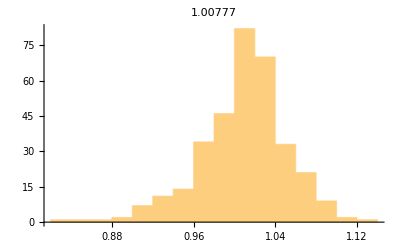

```mathematica
symbol="NYSE:SPY";
ts=FinancialData[
symbol,
"Return",
{CurrentDate[]-Quantity[30,"Years"],CurrentDate[], "Month"}
]//TimeSeriesMap[1+#&,#]&
Histogram[ts, Automatic, PlotLabel->GeometricMean[ts]]
```

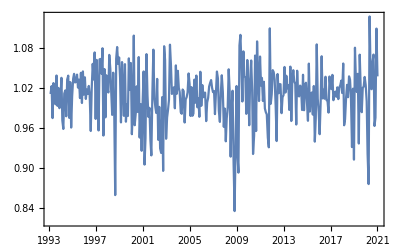

```mathematica
DateListPlot[ts]
```

```mathematica
normalMean=GeometricMean[ts]
```

1.00777

```mathematica
ApplyTailInsurance[
<|
"cost"->cost_,
"strike"->strike_,
"numberOfPuts"->numberOfPuts_,
"cashFraction"->cashFraction_
|>
,ts_
]:=TimeSeriesMap[#*(1-cashFraction)*(1-cost*numberOfPuts)+cashFraction+numberOfPuts*Max[strike-#,0]&,ts];

Manipulate[
Block[{dist},
dist:=ApplyTailInsurance[<|"cost"->cost,"strike"->strike,"numberOfPuts"->numberOfPuts,"cashFraction"->0.01|>,ts];
Histogram[
dist,
Automatic,
PlotLabel->Mean[dist]
]
],
{numberOfPuts,1,10},
{strike,0.85,1},
{cost,0,0.1}
]
```

```mathematica
Manipulate[
Plot[
{
GeometricMean[ApplyTailInsurance[cost, K, 0.25,ts]],
GeometricMean[ApplyTailInsurance[cost, K, 0.50,ts]],
GeometricMean[ApplyTailInsurance[cost, K, 1,ts]],
GeometricMean[ApplyTailInsurance[cost, K, 1.50,ts]],
GeometricMean[ApplyTailInsurance[cost, K, 2,ts]]
},
{K,0.75,1},
PlotLegends->{0.25,0.5,1,1.5,2},
AxesLabel->{"Rel. Strike","Geometric Avg. / Month"},
ImageSize->Large,
PlotLabel->"Monthly Geometric Return for "<>symbol<>" when holding n puts"
],
{cost, 0,0.05}
]
```

```mathematica
ApplyCashAllocation[fractionToAllocateToCash_]:=Function[ alloc,
<|
"stocks"->alloc[["stocks"]]-fractionToAllocateToCash,
"cash"-> (alloc[["cash"]]/._Missing->0) +fractionToAllocateToCash
|>];

ApplyAllStocksAllocation[]:=<|"stocks"->1|>

ApplyPutAllocation[]:=Function[ alloc,
Block[{stocks},
stocks = (alloc[["stocks"]]/._Missing->0);
<|
"stocks"->stocks-premium,
"otmLongPut"-> premium
|>]
];

ApplyAllStocksAllocation[]//ApplyCashAllocation[f]
```

<|stocks→1-3 f,cash→3 f|>